```mathematica
strlatex2= "\\procpaper[switch=45,
title={`title`}, 
   author={`author`}, 
index={`indexstr`}]\n{`file`}\n\n";
stringarea="\\session{`area`}\n\n";

brnames[str_]:=
Module[{lis},lis=StringSplit[str," "];
"\\index{"<>Last[lis]<>", "<>StringTake[StringJoin[(#<>" ")&/@lis[[1;;-2]]],1;;-2]]<>"}"
CapitalizeNames[str_]:=StringRiffle[Capitalize[StringSplit[ToLowerCase[StringReplace[str,","->", "]]," "]]," "]
geraPoster[data_]:=StringTemplate[strlatex2][<|"title"->data[[4]],"author"->CapitalizeNames[data[[5]] ]<>","<>CapitalizeNames@data[[6]] ,"indexstr"->StringJoin[brnames/@StringSplit[CapitalizeNames@data[[5]]<>","<>CapitalizeNames@data[[6]],","]],"file"->(ToString@data[[1]] )|>]
convstr[str_]:=URLDecode[URLEncode[str,CharacterEncoding->"ISO8859-1"]]
liscodsposters={"ED","GE","PE","PR","SB","SW","TP"};
liscodsfull={"FP"};


prefix="/Users/neylemke/Google\ Drive/burocracia/ab3c/proceedings-x-meeting2016/";

lisposter=Import[prefix<>"codes_poster_session_20170206_corrigido.csv","TSV"];
lisposter=Rest[lisposter];
lisareas=Union[lisposter[[All,3]]];


strfile=StringJoin@Table[StringTemplate[stringarea][<|"area"->area|>]<>StringJoin[geraPoster/@Select[lisposter, #[[3]]==area&]],{area,lisareas}];
Export[prefix<>"posters.tex",strfile,"String"]
```

/Users/neylemke/Google Drive/burocracia/ab3c/proceedings-x-meeting2016/posters.tex

```mathematica
lisaut=Table[Union[{data[[5]]},StringSplit[data[[6]],","]],{data, lisposter}];
edges=Union[Table[Select[Flatten[Outer[{#1,#2}&,aut,aut],1],#[[1]]≠#[[2]]&],{aut,lisaut}]];
```

```mathematica
vert=Union[Flatten[edges]];

vertlabel=Table[vert[[i]]->i,{i,1,Length[vert]}];
gr=Union[Flatten[Select[edges,Length[#]>1&],1]]/.{x_,y_}->x<->y;
gr2=Union[Sort/@gr];
```

```mathematica
Length[gr2]
```

2886

```mathematica
tooltip=Tooltip[#]&/@vert;
```

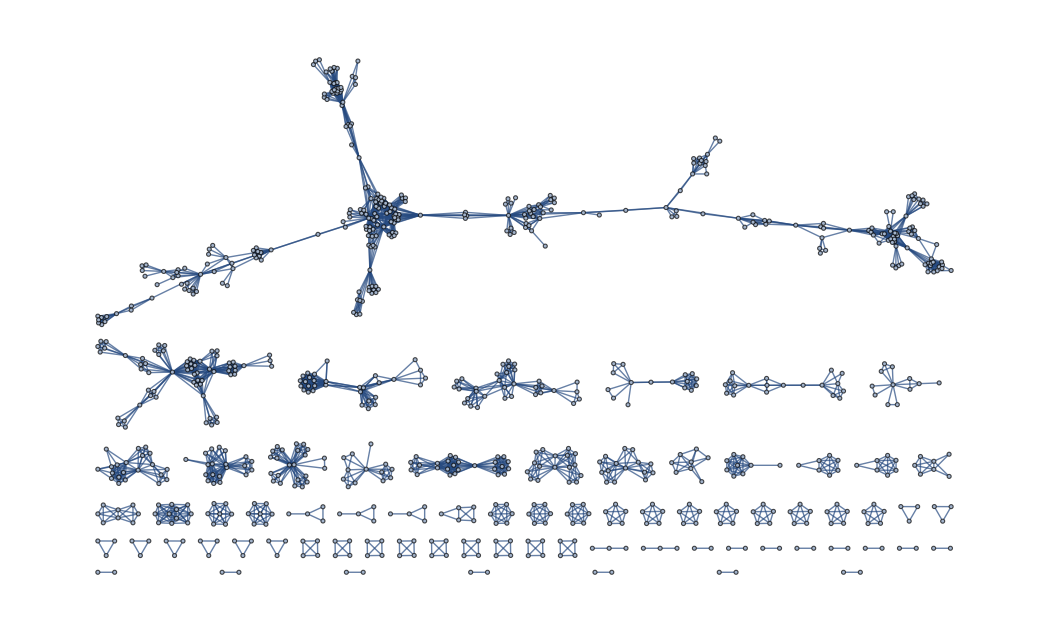

```mathematica
Graph[tooltip,gr2]
```

```mathematica
wordcloud=WordCloud@ToUpperCase@StringDelete[StringJoin[lisposter[[All,4]]] ,{" of ", "in ", " a ", " the ", " to ", " 1 " , " and ", "for ", "with ", "A ", " A"," a","from ", " by ", "1",
 "the", "5","à", " an " , " on ", " A ", "An "}];
```

```mathematica
Export[prefix<>"wordcloud.pdf",wordcloud, "PDF"]
```

/Users/neylemke/Google Drive/burocracia/ab3c/proceedings-x-meeting2016/wordcloud.pdf

Aïda Ouangraoua